```mathematica
Psi[t_,w0_,σ_]:=(2/(σ π))^(1/4)Exp[-t^2/σ-ⅈ w0 t];
Simplify[Integrate[Abs[Psi[t,0,σ]]^2,{t,-∞,∞}],{σ∈Reals,σ>0}]
```

1

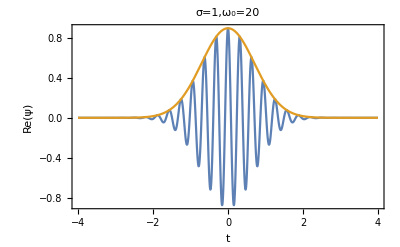

```mathematica
Plot[{Re[Psi[t,20,1]],Re[Psi[t,0,1]]},{t,-4,4},PlotRange->All,Frame->True,FrameLabel->{"t","Re(ψ)"},BaseStyle->{FontSize->14},PlotLabel->"σ=1,ω_0=20"]
```

```mathematica
PMZ=FullSimplify[1/4 Integrate[Abs[Psi[t,w0,σ]+Psi[t-τ,w0,σ]]^2,{t,-∞,∞},Assumptions->{σ∈Reals,σ>0,w0∈Reals,w0>0,τ∈Reals,τ>0}]]
```

1/2 (1+ⅇ^(-τ^2/(2 σ)) Cos[w0 τ])

```mathematica
PHOM=FullSimplify[1/4(1+Abs[Integrate[Psi[t,w0,σ]Conjugate[Psi[t-τ,w0,σ]],{t,-∞,∞},Assumptions->{σ∈Reals,σ>0,w0∈Reals,w0>0,τ∈Reals,τ>0}]]^2),{σ∈Reals,σ>0,w0∈Reals,w0>0,τ∈Reals,τ>0}]
```

1/4 (1+ⅇ^(-τ^2/σ))

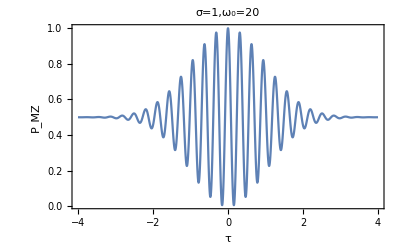

```mathematica
Plot[PMZ /. {w0->20,σ->1},{τ,-4,4},PlotRange->All,Frame->True,FrameLabel->{"τ","P_MZ"},BaseStyle->{FontSize->14},PlotLabel->"σ=1,ω_0=20"]
```

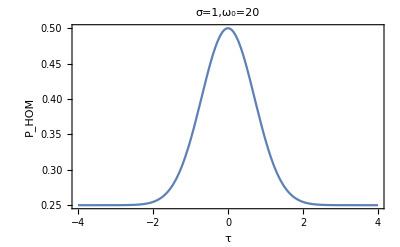

```mathematica
Plot[PHOM /. {w0->20,σ->1},{τ,-4,4},PlotRange->All,Frame->True,FrameLabel->{"τ","P_HOM"},BaseStyle->{FontSize->14},PlotLabel->"σ=1,ω_0=20"]
```